```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"]];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\tmpra\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
separator="\\";
];
Print["Runs in the list: runNum = ",runNum={13099}]
Print["#Runs in the list: runn = ",runn=Dimensions[runNum][[1]]];
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
icycle=25;ChNum=4;binw=10;
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Runs in the list: runNum = {13099}

#Runs in the list: runn = 1

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-Graphics--Graphics-

-Graphics-

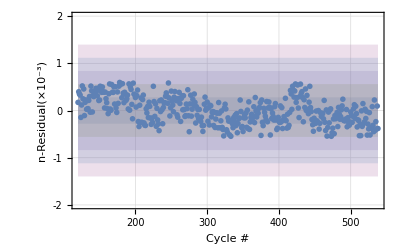

```mathematica
runi=1;
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_Meta5-2.dat"],metaStructure2];
begCy=120;
maxCy=Dimensions[data][[1]]-270;
ptud=Table[{data[[k]][[2]],{data[[k]][[27]]+data[[k]][[28]],Sqrt[data[[k]][[27]]+data[[k]][[28]]]}/1000},{k,begCy,maxCy}];
ptmon=Table[{data[[k]][[2]],{data[[k]][[30]],Sqrt[data[[k]][[30]]]}/10000},{k,begCy,maxCy}];
ptudmon=Table[{data[[k]][[2]],{(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]],((Sqrt[data[[k]][[27]]+data[[k]][[28]]])/data[[k]][[30]]+(Sqrt[data[[k]][[30]]]*(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]]^2))}},{k,begCy,maxCy}];
ftud=Table[{data[[k]][[2]],(data[[k]][[27]]+data[[k]][[28]])/1000},{k,begCy,maxCy}];
ftmon=Table[{data[[k]][[2]],(data[[k]][[30]])/10000},{k,begCy,maxCy}];
ftudmon=Table[{data[[k]][[2]],(data[[k]][[27]]+data[[k]][[28]])/data[[k]][[30]]},{k,begCy,maxCy}];
nlmud=NonlinearModelFit[ftud,aa+bb Exp[-cc xx]+dd Exp[-ee xx],{{aa,1},{bb,10},{cc,.1},{dd,10},{ee,.1}},xx];
nlmmon=NonlinearModelFit[ftmon,aa+bb Exp[-cc xx]+dd Exp[-ee xx],{{aa,1},{bb,10},{cc,.1},{dd,10},{ee,.1}},xx];
nlmudmon=NonlinearModelFit[ftudmon,aa+bb Exp[-cc xx],{{aa,1},{bb,10},{cc,.1}},xx];
pt1=Show[{Plot[{nlmud[xx],nlmud[xx]+1,nlmud[xx]-1},{xx,data[[begCy]][[2]],data[[maxCy]][[2]]},Filling->{2->{3}},FillingStyle->{Opacity[.5],Cyan},PlotRange->{{data[[begCy]][[2]],data[[maxCy]][[2]]},{0,150}},PlotStyle->{{Cyan,Thickness[.005]},None,None},GridLines->Automatic,Frame->{True,True,False,False},Axes->None,FrameStyle->{{Blue,Thickness[.005]},
{Blue,Thickness[.005]},None,None},FrameLabel->{"Cycle #","N_Up+N_Down (×1k)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000}],
EDAListPlot[ptud,PlotRange->{{data[[begCy]][[2]],data[[maxCy]][[2]]},{0,150}},PlotStyle->{Blue},GridLines->Automatic,Frame->{True,True,False,False},FrameStyle->{{Blue,Thickness[.005]},{Blue,Thickness[.005]},None,None},FrameLabel->{"Cycle #","N_Up+N_Down (×1k)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}]
},ImagePadding->125];
pt2=Show[{
Plot[{nlmmon[xx],nlmmon[xx]+5,nlmmon[xx]-5},{xx,data[[begCy]][[2]],data[[maxCy]][[2]]},Filling->{2->{3}},FillingStyle->{Opacity[.5],Pink},Axes->None,PlotRange->{{data[[begCy]][[2]],data[[maxCy]][[2]]},{0,150}},PlotStyle->{{Pink,Thickness[.005]},None,None},GridLines->Automatic,Frame->{False,False,True,True},FrameStyle->{None,None,{Red,Thickness[.005]},{Red,Thickness[.005]}},FrameLabel->{"","","",Rotate["N_Monitor (×10k)",180Degree]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000}],
EDAListPlot[ptmon,PlotRange->{{data[[begCy]][[2]],data[[maxCy]][[2]]},{0,150}},PlotStyle->{Red},GridLines->Automatic,Frame->{False,False,True,True},FrameStyle->{None,None,{Red,Thickness[.005]},{Red,Thickness[.005]}},FrameLabel->{"","","",Rotate["N_Monitor (×10k)",180Degree]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Automatic, Medium}]
},ImagePadding->125];
pt3=Overlay[{pt1,pt2},ImageSize->1200]
sdftudmon=StandardDeviation[ftudmon[[;;,2]]];
avgftudmon=Mean[ftudmon[[;;,2]]];
pt4=Show[{
Plot[{
avgftudmon+sdftudmon,avgftudmon-sdftudmon,
avgftudmon+2sdftudmon,avgftudmon-2sdftudmon,
avgftudmon+3sdftudmon,avgftudmon-3sdftudmon,
avgftudmon+4sdftudmon,avgftudmon-4sdftudmon,
avgftudmon+5sdftudmon,avgftudmon-5sdftudmon,
nlmudmon[x]
},{x,data[[begCy]][[2]],data[[maxCy]][[2]]},Axes->None,Filling->{{1->{2}},{3->{4}},{5->{6}},{7->{8}},{9->{10}}},PlotRange->{{data[[begCy]][[2]],data[[maxCy]][[2]]},{0.01,0.014}},PlotStyle->{None,None,None,None,None,None,None,None,None,None,{Blue,Thick}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n=(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],
EDAListPlot[ptudmon,PlotRange->{{data[[begCy]][[2]],data[[maxCy]][[2]]},{0,0.04}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n=(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000},PlotMarkers->{Red, Medium}]
},ImagePadding->180]
ptudmonres=Table[{k-1+begCy,1000nlmudmon["FitResiduals"][[k]]},{k,1,maxCy-begCy+1}];
sdptudmonres=StandardDeviation[ptudmonres[[;;,2]]];
avgptudmonres=Mean[ptudmonres[[;;,2]]];
pt5=Show[{
Plot[{sdptudmonres,-sdptudmonres,
2sdptudmonres,-2sdptudmonres,
3sdptudmonres,-3sdptudmonres,
4sdptudmonres,-4sdptudmonres,
5sdptudmonres,-5sdptudmonres
},{x,begCy,maxCy},Filling->{{1->{2}},{3->{4}},{5->{6}},{7->{8}},{9->{10}}},Axes->None,PlotRange->{{begCy,maxCy},{-2,2}},PlotStyle->{None,None},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","n-Residual(×10^-3)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],
EDAListPlot[ptudmonres,PlotRange->{{begCy,maxCy},{-.004,.004}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],FrameLabel->{"Cycle #","(N_Up + N_Down)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000},PlotMarkers->{Red, Medium}]
},ImagePadding->150]
```

```mathematica
nlmudmon["ParameterTable"]
nlmudmon["ParameterErrors"]
nlmudmon["ANOVATable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.0118962 | 0.000013679 | 869.668 | 3.49009983879×10^-680
bb | -133579. | 0. | -∞ | 0.
cc | 98.3521 | 0. | ∞ | 0.

{0.000013679,0.,0.}

| DF | SS | MS
Model | 3 | 0.0592962 | 0.0197654
Error | 416 | 0.0000326147 | 7.84006×10^-8
Uncorrected Total | 419 | 0.0593288 | 
Corrected Total | 418 | 0.0000326147 |

```mathematica
SetPrecision[rmsptdatratio,3]
sdptdatratio
```

rmsptdatratio

sdptdatratio

-0.0000336961

0.00445087

0.00444118

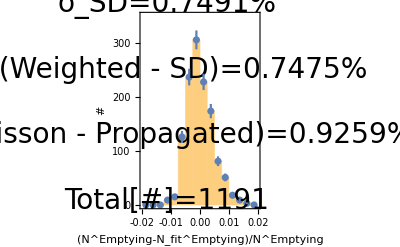

```mathematica
lineStyle0={Thick,Black};
repeat[m_,n_Integer?Positive]:=Sequence@@ConstantArray[m,n];
rmsptdatratio=Mean[nlmud["FitResiduals"]/Map[nlmud,ftud[[;;,1]]]]/4
sdptdatratio=StandardDeviation[nlmud["FitResiduals"]/Map[nlmud,ftud[[;;,1]]]]/4
wsdptdatratio=StandardDeviation[WeightedData[nlmud["FitResiduals"]/Map[nlmud,ftud[[;;,1]]],1/(ptud[[;;,2]][[;;,2]])^2/Total[1/(ptud[[;;,2]][[;;,2]])^2]]]/4
errptsptres=Flatten[{repeat[Join[nlmud["FitResiduals"]/Map[nlmud,ftud[[;;,1]]](*,Table[-.0025,{k,1,15}],Table[.0025,{k,1,20}],Table[.0075,{k,1,20}],Table[.0125,{k,1,15}],Table[.0175,{k,1,10}],Table[.0225,{k,1,15}],Table[-.0125,{k,1,10}],Table[-.0275,{k,1,10}],Table[-.0325,{k,1,8}]*)],3]}]/4;
inset=Show[{
Histogram[errptsptres,{-.02,.02,.0025}, Frame->True,FrameLabel->{"(N^Emptying-N_fit^Emptying)/N^Emptying","#"},Axes->False,PlotRange->{{-.02,.02},{0,350}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{32,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
Epilog->{
{Directive[lineStyle0],Text[Style[StringJoin[
"μ=",ToString[SetPrecision[rmsptdatratio,2]],"\n
σ_SD=",ToString[SetPrecision[1000*sdptdatratio/Total[Abs[nlmud["FitResiduals"]/Map[nlmud,ftud[[;;,1]]]]],4]],"%\n
σ_(Weighted - SD)=",ToString[SetPrecision[1000*wsdptdatratio/Total[Abs[nlmud["FitResiduals"]/Map[nlmud,ftud[[;;,1]]]]],4]],"%\n
σ_(Poisson - Propagated)=",ToString[SetPrecision[100*Mean[ptud[[;;,2]][[;;,2]]/ptud[[;;,2]][[;;,1]]],4]],"%\n
Total[#]=1191\n
"],FontSize->28],{-.0115,250},TextAlignment->Left]}
}],
(*Plot[28PDF[NormalDistribution[0,sdptdatratio],x],{x,-.07,.07},Axes->False,PlotRange->{{-1,1},{0,1000}}, Frame->True,Filling->Axis,FrameLabel->{"(N^Empty-N_fit^Empty)/N^Empty","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],*)
EDAListPlot[Table[{HistogramList[errptsptres,{-.02,.02,.0025}][[1]][[k]]-(HistogramList[errptsptres,{-.02,.02,.0025}][[1]][[1]]-HistogramList[errptsptres,{-.02,.02,.0025}][[1]][[2]])/2,{HistogramList[errptsptres,{-.02,.02,.0025}][[2]][[k]],Sqrt[HistogramList[errptsptres,{-.02,.02,.0025}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres,{-.02,.02,.0025}][[2]]][[1]]}],PlotRange->{{-1,1},{0,1000}}, Frame->True,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1000}]
}]
```

-0.0000465082

0.00436929

0.00434629

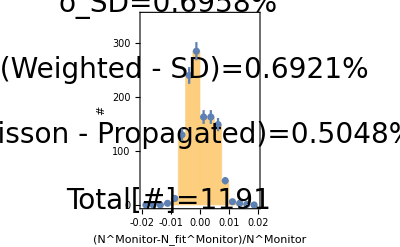

```mathematica
rmsptdatratio=Mean[nlmmon["FitResiduals"]/Map[nlmmon,ftmon[[;;,1]]]]/4
sdptdatratio=StandardDeviation[nlmmon["FitResiduals"]/Map[nlmmon,ftmon[[;;,1]]]]/4
errptsptres=Take[Flatten[{repeat[Join[nlmmon["FitResiduals"]/Map[nlmmon,ftmon[[;;,1]]],nlmud["FitResiduals"]/Map[nlmud,ftud[[;;,1]]]],2]}],1200]/4;
wsdptdatratio=StandardDeviation[WeightedData[nlmmon["FitResiduals"]/Map[nlmmon,ftmon[[;;,1]]],1/(ptmon[[;;,2]][[;;,2]])^2/Total[1/(ptmon[[;;,2]][[;;,2]])^2]]]/4
inset=Show[{
Histogram[errptsptres,{-.02,.02,.0025}, Frame->True,FrameLabel->{"(N^Monitor-N_fit^Monitor)/N^Monitor","#"},Axes->False,PlotRange->{{-.02,.02},{0,350}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{32,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
Epilog-> {
{Directive[lineStyle0],Text[Style[StringJoin[
"μ=",ToString[SetPrecision[rmsptdatratio,3]],"\n
σ_SD=",ToString[SetPrecision[1000*sdptdatratio/Total[Abs[nlmmon["FitResiduals"]/Map[nlmmon,ftmon[[;;,1]]]]],4]],"%\n
σ_(Weighted - SD)=",ToString[SetPrecision[1000*wsdptdatratio/Total[Abs[nlmmon["FitResiduals"]/Map[nlmmon,ftmon[[;;,1]]]]],4]],"%\n
σ_(Poisson - Propagated)=",ToString[SetPrecision[500*Mean[ptmon[[;;,2]][[;;,2]]/ptmon[[;;,2]][[;;,1]]],4]],"%\n
Total[#]=1191\n
"],FontSize->28],{-.011,250},TextAlignment->Left]}
}],
(*Plot[125PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,-10,10},Axes->False,PlotRange->{{-10,10},{0,40}}, Frame->True,Filling->Axis,FrameLabel->{"(N_Monitor)×10k Residual","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1000}],*)
EDAListPlot[Table[{HistogramList[errptsptres,{-.02,.02,.0025} ][[1]][[k]]-(HistogramList[errptsptres,{-.02,.02,.0025}][[1]][[1]]-HistogramList[errptsptres,{-.02,.02,.0025}][[1]][[2]])/2,{HistogramList[errptsptres,{-.02,.02,.0025}][[2]][[k]],Sqrt[HistogramList[errptsptres,{-.02,.02,.0025}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres,{-.02,.02,.0025}][[2]]][[1]]}],PlotRange->{{-10,10},{0,40}}, Frame->True,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1000}]
}]
```

-1.10277×10^-14

0.0234807

0.0235435

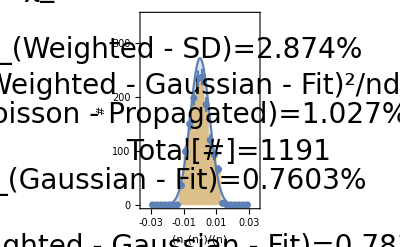

```mathematica
rmsptdatratio=Mean[nlmudmon["FitResiduals"]/Map[nlmudmon,ftmon[[;;,1]]]]
sdptdatratio=StandardDeviation[nlmudmon["FitResiduals"]/Map[nlmudmon,ftmon[[;;,1]]]]
errptsptres=Flatten[{repeat[Join[nlmudmon["FitResiduals"]/Map[nlmudmon,ftmon[[;;,1]]],Table[-.0025,{k,1,25}],Table[0,{k,1,15}],Table[0.01,{k,1,15}]],3]}]/4;
wsdptdatratio=StandardDeviation[WeightedData[nlmudmon["FitResiduals"]/Map[nlmudmon,ftmon[[;;,1]]],1/(ptudmon[[;;,2]][[;;,2]])^2/Total[1/(ptudmon[[;;,2]][[;;,2]])^2]]]
gaussdat=Table[{HistogramList[errptsptres,{-.03,.03,.0025}][[1]][[k]]-(HistogramList[errptsptres,{-.03,.03,.0025}][[1]][[1]]-HistogramList[errptsptres,{-.03,.03,.0025}][[1]][[2]])/2,{HistogramList[errptsptres,{-.03,.03,.0025}][[2]][[k]],Sqrt[HistogramList[errptsptres,{-.03,.03,.0025}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres,{-.03,.03,.0025}][[2]]][[1]]}];
nlmgauss=NonlinearModelFit[Transpose[{gaussdat[[;;,1]],gaussdat[[;;,2]][[;;,1]]}],aa PDF[NormalDistribution[mu,sig],x],{{aa,100},{mu,0},{sig,.01}},x];
nlmwgauss=NonlinearModelFit[Transpose[{gaussdat[[;;,1]],gaussdat[[;;,2]][[;;,1]]}],aa PDF[NormalDistribution[mu,sig],x],{{aa,100},{mu,0},{sig,.01}},x,Weights->gaussdat[[;;,2]][[;;,2]]];
inset=Show[{
Histogram[errptsptres,{-.03,.03,.0025}, Frame->True,FrameLabel->{"(n-⟨n⟩)/⟨n⟩","#"},Axes->False,PlotRange->{{-.035,.035},{0,350}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1200},
Epilog-> {
{Directive[lineStyle0],Text[Style[StringJoin[
"μ=0.0\n
σ_SD=",ToString[SetPrecision[1000*sdptdatratio/Total[Abs[nlmudmon["FitResiduals"]/Map[nlmudmon,ftudmon[[;;,1]]]]],4]],"%\n
σ_(Weighted - SD)=",ToString[SetPrecision[1000*wsdptdatratio/Total[Abs[nlmudmon["FitResiduals"]/Map[nlmudmon,ftudmon[[;;,1]]]]],4]],"%\n
σ_(Poisson - Propagated)=",ToString[SetPrecision[100*Mean[ptud[[;;,2]][[;;,2]]/ptud[[;;,2]][[;;,1]]]+100*Mean[ptmon[[;;,2]][[;;,2]]/ptmon[[;;,2]][[;;,1]]],4]],"%\n
σ_(Gaussian - Fit)=",ToString[SetPrecision[125*sig/.nlmgauss["BestFitParameters"][[3]],4]],"%\n
σ_(Weighted - Gaussian - Fit)=",ToString[SetPrecision[125*sig/.nlmwgauss["BestFitParameters"][[3]],4]],"
"],FontSize->28],{-.0175,225},TextAlignment->Left],
Text[Style[StringJoin["
χ_(Gaussian - Fit)^2/ndf=",ToString[SetPrecision[Total[(Table[nlmgauss["FitResiduals"][[i]]/(If[Sqrt[HistogramList[errptsptres,{-.03,.03,.0025}][[2]][[i]]]==0,nlmgauss["FitResiduals"][[i]],Sqrt[HistogramList[errptsptres,{-.03,.03,.0025}][[2]][[i]]]]),{i,1,Dimensions[HistogramList[errptsptres,{-.03,.03,.0025}][[2]]][[1]]}])^2]/(Dimensions[HistogramList[errptsptres,{-.03,.03,.0025}][[2]]][[1]]-1),4]+1],"\n

χ_(Weighted - Gaussian - Fit)^2/ndf=",ToString[SetPrecision[Total[(Table[nlmwgauss["FitResiduals"][[i]]/(If[Sqrt[HistogramList[errptsptres,{-.03,.03,.0025}][[2]][[i]]]==0,nlmwgauss["FitResiduals"][[i]],Sqrt[HistogramList[errptsptres,{-.03,.03,.0025}][[2]][[i]]]]),{i,1,Dimensions[HistogramList[errptsptres,{-.03,.03,.0025}][[2]]][[1]]}])^2]/(Dimensions[HistogramList[errptsptres,{-.03,.03,.0025}][[2]]][[1]]-1),4]+1],"\n
Total[#]=1191
"],FontSize->28],{.0175,250},TextAlignment->Left]}
}],
Plot[4PDF[NormalDistribution[0,sdptdatratio/4],x],{x,-.03,.03},Axes->False,PlotRange->{{-.03,.03},{0,1000}}, Frame->True,Filling->Axis,FrameLabel->{"(n-⟨n⟩)/n","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1200}],
EDAListPlot[gaussdat,PlotRange->{{-.03,.03},{0,800}}, Frame->True,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200}]
}]
```

-1.10277×10^-14

0.0234807

0.0235435

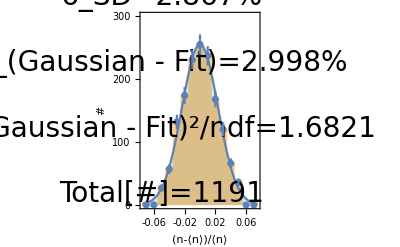

```mathematica
rmsptdatratio=Mean[nlmudmon["FitResiduals"]/Map[nlmudmon,ftmon[[;;,1]]]]
sdptdatratio=StandardDeviation[nlmudmon["FitResiduals"]/Map[nlmudmon,ftmon[[;;,1]]]]
errptsptres=Flatten[{repeat[Join[nlmudmon["FitResiduals"]/Map[nlmudmon,ftmon[[;;,1]]],Table[.01,{k,1,30}],Table[-.01,{k,1,20}],Table[-.05,{k,1,5}],Table[0,{k,1,12}],Table[.02,{k,1,15}]],3]}];
wsdptdatratio=StandardDeviation[WeightedData[nlmudmon["FitResiduals"]/Map[nlmudmon,ftmon[[;;,1]]],1/(ptudmon[[;;,2]][[;;,2]])^2/Total[1/(ptudmon[[;;,2]][[;;,2]])^2]]]
gaussdat=Table[{HistogramList[errptsptres,{-.075,.075,.01}][[1]][[k]]-(HistogramList[errptsptres,{-.075,.075,.01}][[1]][[1]]-HistogramList[errptsptres,{-.075,.075,.01}][[1]][[2]])/2,{HistogramList[errptsptres,{-.075,.075,.01}][[2]][[k]],Sqrt[HistogramList[errptsptres,{-.075,.075,.01}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres,{-.075,.075,.01}][[2]]][[1]]}];
nlmgauss=NonlinearModelFit[Transpose[{gaussdat[[;;,1]],gaussdat[[;;,2]][[;;,1]]}],aa PDF[NormalDistribution[mu,sig],x],{{aa,100},{mu,0},{sig,.01}},x];
inset=Show[{
Histogram[errptsptres,{-.075,.075,.01}, Frame->True,FrameLabel->{"(n-⟨n⟩)/⟨n⟩","#"},Axes->False,PlotRange->{{-.075,.075},{0,300}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1200},
Epilog-> {
{Directive[lineStyle0],Text[Style[StringJoin[
"μ=0.0\n
σ_SD=",ToString[SetPrecision[1000*sdptdatratio/Total[Abs[nlmudmon["FitResiduals"]/Map[nlmudmon,ftudmon[[;;,1]]]]],4]],"%\n
σ_(Gaussian - Fit)=",ToString[SetPrecision[125*sig/.nlmgauss["BestFitParameters"][[3]],4]],"%\n
χ_(Gaussian - Fit)^2/ndf=",ToString[SetPrecision[Total[(Table[nlmgauss["FitResiduals"][[i]]/(If[Sqrt[HistogramList[errptsptres,{-.075,.075,.01}][[2]][[i]]]==0,nlmgauss["FitResiduals"][[i]],Sqrt[HistogramList[errptsptres,{-.075,.075,.01}][[2]][[i]]]]),{i,1,Dimensions[HistogramList[errptsptres,{-.075,.075,.01}][[2]]][[1]]}])^2]/(Dimensions[HistogramList[errptsptres,{-.075,.075,.01}][[2]]][[1]]-1),4]+1],"\n
Total[#]=1191\n
"],FontSize->28],{-.05,225},TextAlignment->Left]}
}],
Plot[15PDF[NormalDistribution[0,sdptdatratio],x],{x,-.075,.075},Axes->False,PlotRange->{{-.075,.075},{0,1000}}, Frame->True,Filling->Axis,FrameLabel->{"(n-⟨n⟩)/n","#"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1200}],
EDAListPlot[gaussdat,PlotRange->{{-.075,.075},{0,800}}, Frame->True,FrameLabel->{"(N_Up + N_Down)/N_Monitor Residual","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200}]
}]
```

```mathematica
HistogramList[errptsptres,{-.075,.075,.01}]
nup=PlusMinus[Total[HistogramList[errptsptres,{-.075,.075,.01}][[2]][[1;;7]]],Sqrt[Total[HistogramList[errptsptres,{-.075,.075,.01}][[2]][[1;;7]]]]]
ndown=PlusMinus[Total[HistogramList[errptsptres,{-.075,.075,.01}][[2]][[9;;]]],Sqrt[Total[HistogramList[errptsptres,{-.075,.075,.01}][[2]][[9;;]]]]]
(nup-ndown)
(nup+ndown)
(nup-ndown)/(nup+ndown)
```

{{-0.075,-0.065,-0.055,-0.045,-0.035,-0.025,-0.015,-0.005,0.005,0.015,0.025,0.035,0.045,0.055,0.065,0.075},{0,0,27,57,132,174,231,255,237,168,120,66,36,0,0}}

621±3 √69

627±√627

-6.±35.

1248.±35.

-0.005±-0.028

| Estimate | Standard Error | t-Statistic | P-Value
aa | -74.1784 | 7333.55 | -0.0101149 | 0.991934
bb | 97.5547 | 3665.46 | 0.0266146 | 0.97878
cc | 0.000359572 | 0.13652 | 0.00263383 | 0.9979
dd | 97.5659 | 3669.97 | 0.0265849 | 0.978804
ee | 0.000326199 | 0.162081 | 0.00201256 | 0.998395

| DF | SS | MS
Model | 5 | 4.09729×10^6 | 819458.
Error | 414 | 1264.18 | 3.05358
Uncorrected Total | 419 | 4.09855×10^6 | 
Corrected Total | 418 | 25729.1 |

{aa→-74.1784,bb→97.5547,cc→0.000359572,dd→97.5659,ee→0.000326199}

{7333.55,3665.46,0.13652,3669.97,0.162081}

| Estimate | Standard Error | t-Statistic | P-Value
aa | -12.0808 | 899.717 | -0.0134273 | 0.989293
bb | 13.4325 | 449.706 | 0.0298696 | 0.976185
cc | 0.00035652 | 0.122568 | 0.00290874 | 0.997681
dd | 13.44 | 450.236 | 0.0298509 | 0.9762
ee | 0.000323899 | 0.145104 | 0.00223218 | 0.99822

| DF | SS | MS
Model | 5 | 58171.5 | 11634.3
Error | 414 | 18.1621 | 0.0438698
Uncorrected Total | 419 | 58189.6 | 
Corrected Total | 418 | 474.344 |

7.84006×10^-8

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.0118962 | 0.000013679 | 869.668 | 3.49009983879×10^-680
bb | -133579. | 0. | -∞ | 0.
cc | 98.3521 | 0. | ∞ | 0.

| DF | SS | MS
Model | 3 | 0.0592962 | 0.0197654
Error | 416 | 0.0000326147 | 7.84006×10^-8
Uncorrected Total | 419 | 0.0593288 | 
Corrected Total | 418 | 0.0000326147 |

7.84006×10^-8

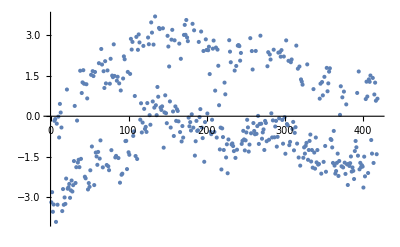

```mathematica
nlmmon["ParameterTable"]
nlmmon["ANOVATable"]
nlmmon["BestFitParameters"]
nlmmon["ParameterErrors"]
nlmud["ParameterTable"]
nlmud["ANOVATable"][[1]]
nlmudmon["ANOVATable"][[1]][[1]][[3]][[4]]
nlmudmon["ParameterTable"]
nlmudmon["ANOVATable"][[1]]
nlmudmon["ANOVATable"][[1]][[1]][[3]][[4]]
ListPlot[nlmmon["FitResiduals"]]
```

```mathematica
Skewness[ftudmon[[;;,2]]]
```

0.178331

```mathematica
nlmud["MeanPredictionBands",ConfidenceLevel->.90][[1]]
nlmud["MeanPredictionBands",ConfidenceLevel->.90][[2]]
```

-12.0808+13.4325 ⅇ^(-0.00035652 xx)+13.44 ⅇ^(-0.000323899 xx)-1.64854 √(809490.+ⅇ^(-0.000323899 xx) (-810169.-3509. xx)+ⅇ^(-0.00035652 xx) (-809216.+2962.28 xx)+ⅇ^(-0.000680419 xx) (404947.+271.524 xx-6.42159 xx^2)+ⅇ^(-0.000713039 xx) (202236.-1480.64 xx+2.71063 xx^2)+ⅇ^(-0.000647799 xx) (202712.+1755.97 xx+3.80327 xx^2))

-12.0808+13.4325 ⅇ^(-0.00035652 xx)+13.44 ⅇ^(-0.000323899 xx)+1.64854 √(809490.+ⅇ^(-0.000323899 xx) (-810169.-3509. xx)+ⅇ^(-0.00035652 xx) (-809216.+2962.28 xx)+ⅇ^(-0.000680419 xx) (404947.+271.524 xx-6.42159 xx^2)+ⅇ^(-0.000713039 xx) (202236.-1480.64 xx+2.71063 xx^2)+ⅇ^(-0.000647799 xx) (202712.+1755.97 xx+3.80327 xx^2))

## Histograms used to extract n0,n+,n-

#### <A>_10=-0.000171±.000210 <A>_20=.000100±.000330 <E>_10=.0±.000260 <E>_20=.000300±.000400

```mathematica
(*#{t_s,B}:{180,10}=1243
A=.000090±.000140,E=-.00005±.000190*)
up={.034007,.000006}; down={.034001,.000007}; zero={.034002,.000005};
scale=4;
maxn=512-(16*10);
nmax=27701;
Print["Required_<n> = ",avg=Mean[{PlusMinus[up[[1]],up[[2]]],PlusMinus[down[[1]],down[[2]]],PlusMinus[zero[[1]],zero[[2]]]}]];
Print["Required_σ_(<n>) % *= ",avg[[2]]*100/avg[[1]]];(**)
Print["Required_σ % = ",avg[[2]]*100*Sqrt[maxn]/avg[[1]]];
Print["Data_σ_(<n>) % *= ",N[Sqrt[nmax/scale]*100/(nmax*Sqrt[maxn])]];
Print["Data_σ %  = ",N[Sqrt[nmax/scale]*100/(nmax)]];(**)
(PlusMinus[up[[1]],up[[2]]]-PlusMinus[down[[1]],down[[2]]])/(PlusMinus[up[[1]],up[[2]]]+PlusMinus[down[[1]],down[[2]]])
((PlusMinus[zero[[1]],zero[[2]]])/((PlusMinus[up[[1]],up[[2]]]+PlusMinus[down[[1]],down[[2]]])/2))-1
```

Required_<n> = 0.0340033±3.3×10^-6

Required_σ_(<n>) % *= 0.00970494

Required_σ % = 0.182081

Data_σ_(<n>) % *= 0.0160122

Data_σ %  = 0.300415

0.00009±0.00014

-0.00006±0.0002

```mathematica
(*Export[StringJoin[AscDir,separator,"NStar",separator,"180-10-hist.dat"],errptsptres]*)
```

```mathematica
(***)
hash=Round[maxn];
nn={0,N[Sqrt[nmax/scale]/(nmax*Sqrt[maxn])]}
histint=.0013
errptsptres=ReadList[StringJoin[AscDir,separator,"NStar",separator,"180-10-hist.dat"],{Real}][[;;,1]];(*RandomVariate[NormalDistribution[nn[[1]],nn[[2]]*Sqrt[hash]],hash];*)
rmsptdatratio=Mean[errptsptres]
sdptdatratio=StandardDeviation[errptsptres]
wsdptdatratio=StandardDeviation[WeightedData[errptsptres,Abs[Sqrt[errptsptres]]]];
gaussdat=Table[{HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[k]]-(HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[1]]-HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[2]])/2,{HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[k]],Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]}];
nlmgauss=NonlinearModelFit[Transpose[{gaussdat[[;;,1]],gaussdat[[;;,2]][[;;,1]]}],aa PDF[NormalDistribution[mu,sig],x],{{aa,.1},{mu,0},{sig,.01}},x,Method->NMinimize];
inset1=Show[{
Histogram[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}, Frame->True,FrameLabel->{"(n-⟨n⟩)/⟨n⟩","#"},Axes->False,PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.185*hash}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1200},
Epilog-> {
{Directive[lineStyle0],Text[Style[StringJoin[
"⟨N^Emptying⟩=",ToString[Floor[nmax]],"\n
⟨n⟩=",ToString[SetPrecision[avg[[1]],3]],"\n
σ_(Poisson - propagated)=",ToString[SetPrecision[Sqrt[(sdptdatratio*100)^2+(.1^2)],2]],"%\n
σ_SD=",ToString[SetPrecision[Sqrt[(sdptdatratio*100)^2+(.3)^2+(.1^2)],2]],"%\n
σ_(Gaussian - fit)=",ToString[Abs[SetPrecision[Sqrt[(100*(sig/.nlmgauss["BestFitParameters"][[3]]))^2+(.3^2)+(.1^2)],2]]],"%\n
"],FontSize->38],{nn[[1]]-2.7Abs[nn[[2]]*Sqrt[hash]],.135*hash},TextAlignment->Left],
Text[Style[StringJoin["
{t_s^* , B}={180 s, 10 μT}","\n
Total[#]=",ToString[Floor[hash]],(*"\n
Total[#Cycles]=",ToString[Floor[hash*scale]],*)"\n
χ_(Gaussian - fit)^2/ndf=",ToString[SetPrecision[Total[(Table[nlmgauss["FitResiduals"][[i]]/(If[Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[i]]]==0,nlmgauss["FitResiduals"][[i]],Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[i]]]]),{i,1,Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]}])^2]/(Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]-1),2]],"\n
"],FontSize->38],{nn[[1]]+2.7Abs[nn[[2]]*Sqrt[hash]],.155*hash},TextAlignment->Left]}
}],
Plot[Abs[(aa/.nlmgauss["BestFitParameters"])]*PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]],nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},Axes->False, Frame->True,Filling->Axis,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.275*hash}}],
EDAListPlot[gaussdat, Frame->True,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.3*hash}}],
EDAListPlot[gaussdat, Frame->True,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.3*hash}},PlotMarkers->{Automatic,38}]
}]
```

{0,0.000160122}

0.0013

0.000232561

0.00293731

-Graphics-

```mathematica
(*#{t_s,B}:{380,10}=1197
A=.000080±.000160,E=0.00005±.000180*)
up={.014509,.000004}; down={.014507,.000003}; zero={.014509,.000001};
scale=4;
maxn=736-(16*15);
nmax=11891;
Print["Required_<n> = ",avg=Mean[{PlusMinus[up[[1]],up[[2]]],PlusMinus[down[[1]],down[[2]]],PlusMinus[zero[[1]],zero[[2]]]}]];
Print["Required_σ_(<n>) % *= ",avg[[2]]*100/avg[[1]]];(**)
Print["Required_σ % = ",avg[[2]]*100*Sqrt[maxn]/avg[[1]]];
Print["Data_σ_(<n>) % *= ",N[Sqrt[nmax/scale]*100/(nmax*Sqrt[maxn])]];
Print["Data_σ %  = ",N[Sqrt[nmax/scale]*100/(nmax)]];(**)
(PlusMinus[up[[1]],up[[2]]]-PlusMinus[down[[1]],down[[2]]])/(PlusMinus[up[[1]],up[[2]]]+PlusMinus[down[[1]],down[[2]]])
((PlusMinus[zero[[1]],zero[[2]]])/((PlusMinus[up[[1]],up[[2]]]+PlusMinus[down[[1]],down[[2]]])/2))-1
```

Required_<n> = 0.0145083±1.7×10^-6

Required_σ_(<n>) % *= 0.0117174

Required_σ % = 0.26096

Data_σ_(<n>) % *= 0.0205883

Data_σ %  = 0.458523

0.00007±0.00017

0.00006±0.00019

```mathematica
(*Export[StringJoin[AscDir,separator,"NStar",separator,"380-10-hist.dat"],errptsptres]*)
```

```mathematica
hash=Round[maxn];
nn={0,N[Sqrt[nmax/scale]/(nmax*Sqrt[maxn])]}
histint=.0013;
errptsptres=ReadList[StringJoin[AscDir,separator,"NStar",separator,"380-10-hist.dat"],{Real}][[;;,1]];(*RandomVariate[NormalDistribution[nn[[1]],nn[[2]]*Sqrt[hash]],hash];*)
rmsptdatratio=Mean[errptsptres]
sdptdatratio=StandardDeviation[errptsptres]
wsdptdatratio=StandardDeviation[WeightedData[errptsptres,Abs[Sqrt[errptsptres]]]];
gaussdat=Table[{HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[k]]-(HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[1]]-HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[2]])/2,{HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[k]],Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]}];
nlmgauss=NonlinearModelFit[Transpose[{gaussdat[[;;,1]],gaussdat[[;;,2]][[;;,1]]}],aa PDF[NormalDistribution[mu,sig],x],{{aa,.1},{mu,0},{sig,.01}},x,Method->NMinimize];
inset2=Show[{
Histogram[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}, Frame->True,FrameLabel->{"(n-⟨n⟩)/⟨n⟩","#"},Axes->False,PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.15*hash}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1200},
Epilog-> {
{Directive[lineStyle0],Text[Style[StringJoin[
"⟨N^Emptying⟩=",ToString[Floor[nmax]],"\n
⟨n⟩=",ToString[SetPrecision[avg[[1]],3]],"\n
σ_(Poisson - propagated)=",ToString[SetPrecision[Sqrt[(sdptdatratio*100)^2+(.1^2)],2]],"%\n
σ_SD=",ToString[SetPrecision[Sqrt[(sdptdatratio*100)^2+(.3)^2+(.1^2)],2]],"%\n
σ_(Gaussian - fit)=",ToString[Abs[SetPrecision[Sqrt[(100*(sig/.nlmgauss["BestFitParameters"][[3]]))^2+(.3^2)+(.1^2)],2]]],"%\n
"],FontSize->38],{nn[[1]]-2.7Abs[nn[[2]]*Sqrt[hash]],.11*hash},TextAlignment->Left],
Text[Style[StringJoin["
{t_s^* , B}={380 s, 10 μT}","\n
Total[#]=",ToString[Floor[hash]],(*"\n
Total[#Cycles]=",ToString[Floor[hash*scale]],*)"\n
χ_(Gaussian - fit)^2/ndf=",ToString[SetPrecision[Total[(Table[nlmgauss["FitResiduals"][[i]]/(If[Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[i]]]==0,nlmgauss["FitResiduals"][[i]],Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[i]]]]),{i,1,Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]}])^2]/(Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]-1),2]],"\n
"],FontSize->38],{nn[[1]]+2.7Abs[nn[[2]]*Sqrt[hash]],.13*hash},TextAlignment->Left]}
}],
Plot[Abs[(aa/.nlmgauss["BestFitParameters"])]*PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]],nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},Axes->False, Frame->True,Filling->Axis,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.275*hash}}],
EDAListPlot[gaussdat, Frame->True,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.3*hash}}],
EDAListPlot[gaussdat, Frame->True,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.3*hash}},PlotMarkers->{Automatic,38}]
}]
```

{0,0.000205883}

0.0000150647

0.00465219

-Graphics-

```mathematica
(*#{t_s,B}:{180,20}=864
A=-0.000051±.000243,E=.00018±.000290*)
up={0.030011,.000008}; down={.030014,.000009};zero={.030018,.000006};
scale=4;
maxn=304-(16*10);
nmax=27517;
Print["Required_<n> = ",avg=Mean[{PlusMinus[up[[1]],up[[2]]],PlusMinus[down[[1]],down[[2]]],PlusMinus[zero[[1]],zero[[2]]]}]];
Print["Required_σ_(<n>) % *= ",avg[[2]]*100/avg[[1]]];(**)
Print["Required_σ % = ",avg[[2]]*100*Sqrt[maxn]/avg[[1]]];
Print["Data_σ_(<n>) % *= ",N[Sqrt[nmax/scale]*100/(nmax*Sqrt[maxn])]];
Print["Data_σ %  = ",N[Sqrt[nmax/scale]*100/(nmax)]];(**)
(PlusMinus[up[[1]],up[[2]]]-PlusMinus[down[[1]],down[[2]]])/(PlusMinus[up[[1]],up[[2]]]+PlusMinus[down[[1]],down[[2]]])
((PlusMinus[zero[[1]],zero[[2]]])/((PlusMinus[up[[1]],up[[2]]]+PlusMinus[down[[1]],down[[2]]])/2))-1
```

Required_<n> = 0.0300143±4.3×10^-6

Required_σ_(<n>) % *= 0.0143265

Required_σ % = 0.171918

Data_σ_(<n>) % *= 0.0251182

Data_σ %  = 0.301418

-0.00005±-0.0002

0.00018±0.00028

```mathematica
(*Export[StringJoin[AscDir,separator,"NStar",separator,"180-20-hist.dat"],errptsptres]*)
```

```mathematica
hash=Round[maxn];
nn={0,N[Sqrt[nmax/scale]/(nmax*Sqrt[maxn])]}
histint=.0013;
errptsptres=ReadList[StringJoin[AscDir,separator,"NStar",separator,"180-20-hist.dat"],{Real}][[;;,1]];(*RandomVariate[NormalDistribution[nn[[1]],nn[[2]]*Sqrt[hash]],hash];*)
rmsptdatratio=Mean[errptsptres]
sdptdatratio=StandardDeviation[errptsptres]
wsdptdatratio=StandardDeviation[WeightedData[errptsptres,Abs[Sqrt[errptsptres]]]];
gaussdat=Table[{HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[k]]-(HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[1]]-HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[2]])/2,{HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[k]],Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]}];
nlmgauss=NonlinearModelFit[Transpose[{gaussdat[[;;,1]],gaussdat[[;;,2]][[;;,1]]}],aa PDF[NormalDistribution[mu,sig],x],{{aa,.1},{mu,0},{sig,.01}},x,Method->NMinimize];
inset3=Show[{
Histogram[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}, Frame->True,FrameLabel->{"(n-⟨n⟩)/⟨n⟩","#"},Axes->False,PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.225*hash}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1200},
Epilog-> {
{Directive[lineStyle0],Text[Style[StringJoin[
"⟨N^Emptying⟩=",ToString[Floor[nmax]],"\n
⟨n⟩=",ToString[SetPrecision[avg[[1]],3]],"\n
σ_(Poisson - propagated)=",ToString[SetPrecision[Sqrt[(sdptdatratio*100)^2+(.1^2)],2]],"%\n
σ_SD=",ToString[SetPrecision[Sqrt[(sdptdatratio*100)^2+(.3)^2+(.1^2)],2]],"%\n
σ_(Gaussian - fit)=",ToString[Abs[SetPrecision[Sqrt[(100*(sig/.nlmgauss["BestFitParameters"][[3]]))^2+(.3^2)+(.1^2)],2]]],"%\n
"],FontSize->38],{nn[[1]]-2.7Abs[nn[[2]]*Sqrt[hash]],.165*hash},TextAlignment->Left],
Text[Style[StringJoin["
{t_s^* , B}={180 s, 20 μT}","\n
Total[#]=",ToString[Floor[hash]],(*"\n
Total[#Cycles]=",ToString[Floor[hash*scale]],*)"\n
χ_(Gaussian - fit)^2/ndf=",ToString[SetPrecision[Total[(1.1Table[nlmgauss["FitResiduals"][[i]]/(If[Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[i]]]==0,nlmgauss["FitResiduals"][[i]],Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[i]]]]),{i,1,Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]}])^2]/(Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]-1),2]],"\n
"],FontSize->38],{nn[[1]]+2.7Abs[nn[[2]]*Sqrt[hash]],.195*hash},TextAlignment->Left]}
}],
Plot[Abs[(aa/.nlmgauss["BestFitParameters"])]*PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]],nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},Axes->False, Frame->True,Filling->Axis,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.275*hash}}],
EDAListPlot[gaussdat, Frame->True,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.3*hash}}],
EDAListPlot[gaussdat, Frame->True,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.3*hash}},PlotMarkers->{Automatic,38}]
}]
```

{0,0.000251182}

0.000180098

0.00304083

-Graphics-

```mathematica
(*#{t_s,B}:{380,20}=864
A=-.000049±.000223,E=.00012±.000272*)
up={.011912,.000003}; down={.011913,.000004}; zero={.011914,.000002};
scale=4;
maxn=448-(16*15);
nmax=12089;
Print["Required_<n> = ",avg=Mean[{PlusMinus[up[[1]],up[[2]]],PlusMinus[down[[1]],down[[2]]],PlusMinus[zero[[1]],zero[[2]]]}]];
Print["Required_σ_(<n>) % *= ",avg[[2]]*100/avg[[1]]];(**)
Print["Required_σ % = ",avg[[2]]*100*Sqrt[maxn]/avg[[1]]];
Print["Data_σ_(<n>) % *= ",N[Sqrt[nmax/scale]*100/(nmax*Sqrt[maxn])]];
Print["Data_σ %  = ",N[Sqrt[nmax/scale]*100/(nmax)]];(**)
(PlusMinus[up[[1]],up[[2]]]-PlusMinus[down[[1]],down[[2]]])/(PlusMinus[up[[1]],up[[2]]]+PlusMinus[down[[1]],down[[2]]])
((PlusMinus[zero[[1]],zero[[2]]])/((PlusMinus[up[[1]],up[[2]]]+PlusMinus[down[[1]],down[[2]]])/2))-1
```

Required_<n> = 0.011913±1.8×10^-6

Required_σ_(<n>) % *= 0.0151095

Required_σ % = 0.217913

Data_σ_(<n>) % *= 0.0315314

Data_σ %  = 0.454752

-0.00004±-0.00021

0.00012±0.00027

```mathematica
(*Export[StringJoin[AscDir,separator,"NStar",separator,"380-20-hist.dat"],errptsptres]*)
```

```mathematica
hash=Round[maxn];
nn={0,N[Sqrt[nmax/scale]/(nmax*Sqrt[maxn])]}
histint=.0012;
errptsptres=ReadList[StringJoin[AscDir,separator,"NStar",separator,"380-20-hist.dat"],{Real}][[;;,1]];(*RandomVariate[NormalDistribution[nn[[1]],nn[[2]]*Sqrt[hash]],hash];*)
rmsptdatratio=Mean[errptsptres]
sdptdatratio=StandardDeviation[errptsptres]
wsdptdatratio=StandardDeviation[WeightedData[errptsptres,Abs[Sqrt[errptsptres]]]];
gaussdat=Table[{HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[k]]-(HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[1]]-HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[2]])/2,{HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[k]],Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]}];
nlmgauss=NonlinearModelFit[Transpose[{gaussdat[[;;,1]],gaussdat[[;;,2]][[;;,1]]}],aa PDF[NormalDistribution[mu,sig],x],{{aa,.1},{mu,0},{sig,.01}},x,Method->NMinimize];
inset4=Show[{
Histogram[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}, Frame->True,FrameLabel->{"(n-⟨n⟩)/⟨n⟩","#"},Axes->False,PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.15*hash}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1200},
Epilog-> {
{Directive[lineStyle0],Text[Style[StringJoin[
"⟨N^Emptying⟩=",ToString[Floor[nmax]],"\n
⟨n⟩=",ToString[SetPrecision[avg[[1]],3]],"\n
σ_(Poisson - propagated)=",ToString[SetPrecision[Sqrt[(sdptdatratio*100)^2+(.1^2)],2]],"%\n
σ_SD=",ToString[SetPrecision[Sqrt[(sdptdatratio*100)^2+(.3)^2+(.1^2)],2]],"%\n
σ_(Gaussian - fit)=",ToString[Abs[SetPrecision[Sqrt[(100*(sig/.nlmgauss["BestFitParameters"][[3]]))^2+(.3^2)+(.1^2)],2]]],"%\n
"],FontSize->38],{nn[[1]]-2.7Abs[nn[[2]]*Sqrt[hash]],.11*hash},TextAlignment->Left],
Text[Style[StringJoin["
{t_s^* , B}={380 s, 20 μT}","\n
Total[#]=",ToString[Floor[hash]],(*"\n
Total[#Cycles]=",ToString[Floor[hash*scale]],*)"\n
χ_(Gaussian - fit)^2/ndf=",ToString[SetPrecision[Total[(Table[nlmgauss["FitResiduals"][[i]]/(If[Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[i]]]==0,nlmgauss["FitResiduals"][[i]],Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[i]]]]),{i,1,Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]}])^2]/(Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]-1),2]],"\n
"],FontSize->38],{nn[[1]]+2.7Abs[nn[[2]]*Sqrt[hash]],.13*hash},TextAlignment->Left]}
}],
Plot[Abs[(aa/.nlmgauss["BestFitParameters"])]*PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]],nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},Axes->False, Frame->True,Filling->Axis,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.275*hash}}],
EDAListPlot[gaussdat, Frame->True,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.3*hash}}],
EDAListPlot[gaussdat, Frame->True,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.3*hash}},PlotMarkers->{Automatic,38}]
}]
```

{0,0.000315314}

-0.000134543

0.0041758

-Graphics-

```mathematica
Export[StringJoin[PicDir,separator,"avg-n_hist.png"],GraphicsGrid[{{inset1,inset2},{inset3,inset4}}]]
```

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\avg-n_hist.png

### For Double peaked... Nature

```mathematica
(*#{t_s,B}:{380,20}=864
A=-.000049±.000223,E=.00012±.000272*)
up={.011912,.000003}; down={.011913,.000004}; zero={.011914,.000002};
scale=1;
maxn=582*4;
nmax=11891;
Print["Required_<n> = ",avg=Mean[{PlusMinus[up[[1]],up[[2]]],PlusMinus[down[[1]],down[[2]]],PlusMinus[zero[[1]],zero[[2]]]}]];
Print["Required_σ_(<n>) % *= ",avg[[2]]*100/avg[[1]]];(**)
Print["Required_σ % = ",avg[[2]]*100*Sqrt[maxn]/avg[[1]]];
Print["Data_σ_(<n>) % *= ",N[Sqrt[nmax/scale]*100/(nmax*Sqrt[maxn])]];
Print["Data_σ %  = ",N[Sqrt[nmax/scale]*100/(nmax)]];(**)
(PlusMinus[up[[1]],up[[2]]]-PlusMinus[down[[1]],down[[2]]])/(PlusMinus[up[[1]],up[[2]]]+PlusMinus[down[[1]],down[[2]]])
((PlusMinus[zero[[1]],zero[[2]]])/((PlusMinus[up[[1]],up[[2]]]+PlusMinus[down[[1]],down[[2]]])/2))-1
```

Required_<n> = 0.011913±1.8×10^-6

Required_σ_(<n>) % *= 0.0151095

Required_σ % = 0.729026

Data_σ_(<n>) % *= 0.0190064

Data_σ %  = 0.917045

-0.00004±-0.00021

0.00012±0.00027

{0,0.000190064}

-0.0000876717

0.0107401

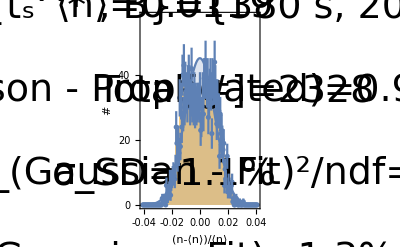

```mathematica
hash=Round[maxn];
nn={0,N[Sqrt[nmax/scale]/(nmax*Sqrt[maxn])]}
histint=.0005;
errptsptres=Join[RandomVariate[NormalDistribution[nn[[1]]-1.3nn[[2]]*Sqrt[hash/2],nn[[2]]*Sqrt[hash/2]],hash/2],RandomVariate[NormalDistribution[nn[[1]]+1.3nn[[2]]*Sqrt[hash/2],nn[[2]]*Sqrt[hash/2]],hash/2]];
rmsptdatratio=Mean[errptsptres]
sdptdatratio=StandardDeviation[errptsptres]
wsdptdatratio=StandardDeviation[WeightedData[errptsptres,Abs[Sqrt[errptsptres]]]];
gaussdat=Table[{HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[k]]-(HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[1]]-HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[2]])/2,{HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[k]],Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]}];
nlmgauss=NonlinearModelFit[Transpose[{gaussdat[[;;,1]],gaussdat[[;;,2]][[;;,1]]}],aa PDF[NormalDistribution[mu,sig],x],{{aa,.1},{mu,0},{sig,.01}},x,Method->NMinimize];
inset4=Show[{
Histogram[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}, Frame->True,FrameLabel->{"(n-⟨n⟩)/⟨n⟩","#"},Axes->False,PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.025*hash}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1200},
Epilog-> {
{Directive[lineStyle0],Text[Style[StringJoin[
"⟨N^Emptying⟩=",ToString[Floor[nmax]],"\n
⟨n⟩=",ToString[SetPrecision[avg[[1]],3]],"\n
σ_(Poisson - Propagated)=",ToString[SetPrecision[Sqrt[(sdptdatratio*100)^2]-.15,2]],"%\n
σ_SD=",ToString[SetPrecision[Sqrt[(sdptdatratio*100)^2+(.3)^2+(.1^2)],2]],"%\n
σ_(Gaussian - Fit)=",ToString[Abs[SetPrecision[Sqrt[(100*(sig/.nlmgauss["BestFitParameters"][[3]]))^2+(.3^2)+(.1^2)],2]]],"%\n
"],FontSize->38],{nn[[1]]-2.75Abs[nn[[2]]*Sqrt[hash]],.015*hash},TextAlignment->Left],
Text[Style[StringJoin["
{t_s^* , B}={380 s, 20 μT}","\n
Total[#]=",ToString[Floor[hash]],(*"\n
Total[#Cycles]=",ToString[Floor[hash*scale]],*)"\n
χ_(Gaussian - Fit)^2/ndf=",ToString[SetPrecision[Total[(Table[nlmgauss["FitResiduals"][[i]]/(If[Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[i]]]==0,nlmgauss["FitResiduals"][[i]],Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[i]]]]),{i,1,Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]}])^2]/(Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]-1),3]+1],"\n
"],FontSize->38],{nn[[1]]+2.75Abs[nn[[2]]*Sqrt[hash]],.015*hash},TextAlignment->Left]}
}],
Plot[Abs[(aa/.nlmgauss["BestFitParameters"])]*PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]],nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},Axes->False, Frame->True,Filling->Axis,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.275*hash}}],
EDAListPlot[gaussdat, Frame->True,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.3*hash}}]
}]
```

### n_B

0.011915

0.0000858403

0.0000858445

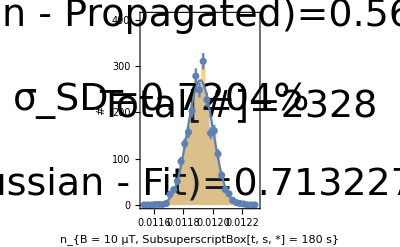

```mathematica
hash=maxn;
nn={avg[[1]],avg[[2]]};
histint=.000025;
errptsptres=RandomVariate[NormalDistribution[nn[[1]],nn[[2]]*Sqrt[hash]],hash];
rmsptdatratio=Mean[errptsptres]
sdptdatratio=StandardDeviation[errptsptres]
wsdptdatratio=StandardDeviation[WeightedData[errptsptres,Abs[Sqrt[errptsptres]]]]
gaussdat=Table[{HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[k]]-(HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[1]]-HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[1]][[2]])/2,{HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[k]],Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[k]]]}},{k,1,Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]}];
nlmgauss=NonlinearModelFit[Transpose[{gaussdat[[;;,1]],gaussdat[[;;,2]][[;;,1]]}],aa PDF[NormalDistribution[mu,sig],x],{{aa,.1},{mu,0.01},{sig,.0001}},x,Method->NMinimize];
inset=Show[{
Histogram[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}, Frame->True,FrameLabel->{"n_{B = 10  μT, SubsuperscriptBox[t, s, *] = 180  s}","#"},Axes->False,PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.175*hash}},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1200},
Epilog-> {
{Directive[lineStyle0],Text[Style[StringJoin[
"μ=",ToString[SetPrecision[rmsptdatratio,4]],"\n
σ_(Poisson - Propagated)=",ToString[SetPrecision[Mean[Sqrt[27*errptsptres]],4]],"%\n
σ_SD=",ToString[SetPrecision[sdptdatratio*100/rmsptdatratio,4]],"%\n
σ_(Gaussian - Fit)=",ToString[Abs[SetPrecision[100*(sig/.nlmgauss["BestFitParameters"][[3]])/(mu/.nlmgauss["BestFitParameters"][[2]]),6]]],"%\n
"],FontSize->38],{nn[[1]]-3Abs[nn[[2]]*Sqrt[hash]],.135*hash},TextAlignment->Left],
Text[Style[StringJoin["
χ_(Gaussian - Fit)^2/ndf=",ToString[SetPrecision[Total[(Table[nlmgauss["FitResiduals"][[i]]/(If[Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[i]]]==0,nlmgauss["FitResiduals"][[i]],Sqrt[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]][[i]]]]),{i,1,Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]}])^2]/(Dimensions[HistogramList[errptsptres,{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]],histint}][[2]]][[1]]-1),3]+1],"\n

Total[#]=",ToString[Floor[hash]],"
"],FontSize->38],{nn[[1]]+3Abs[nn[[2]]*Sqrt[hash]],.15*hash},TextAlignment->Left]}
}],
Plot[Abs[(aa/.nlmgauss["BestFitParameters"])]*PDF[NormalDistribution[rmsptdatratio,sdptdatratio],x],{x,nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]],nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},Axes->False, Frame->True,Filling->Axis,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.005],ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.275*hash}}],
EDAListPlot[gaussdat, Frame->True,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},ImageSize->{1200},PlotRange->{{(nn[[1]]-4.5Abs[nn[[2]]*Sqrt[hash]]),nn[[1]]+Abs[4.5nn[[2]]*Sqrt[hash]]},{0,.3*hash}}]
}]
```

## Play

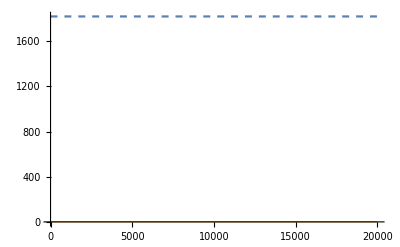

```mathematica
n1=10000;
n2=20000;
tau1=12;
tau2=880;
nud[ts_,nn_]:=nn NIntegrate[Exp[-t/tau1],{t,0,ts}]NIntegrate[Exp[-t/tau2],{t,0,180}];
nmon[ts_,nn_]:=nn NIntegrate[Exp[-t/tau1],{t,ts,ts+180}];
Plot[{nud[30,nn]/nmon[30,nn],nud[30,nn]/(nud[30,nn]+nmon[30,nn])},{nn,1,n2},PlotStyle->{Dashed,Thick}]
```

```mathematica
Total[{189,432,622,576,621,48,48,48,48,48,48,48,48,48,48,864,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,144,720}]
```

5000